```mathematica
CloseStreams[];vals=Table[{tuple,BetterRatioFor[tuple]}
, {tuple, Select[Flatten[Table[SuccessiveTuple[first,l],{first,2,8}, {l,2,5}],1],magicGraham[#]>0&]}]
```

$Aborted

```mathematica
Select[Flatten[Table[SuccessiveTuple[first,l],{first,2,8}, {l,2,4}],1],magicGraham[#]>0&]
```

{{3,5},{3,5,7},{5,7},{5,7,11},{7,11},{7,11,13},{11,13},{11,13,17},{11,13,17,19},{13,17},{13,17,19},{13,17,19,23},{17,19},{17,19,23},{17,19,23,29},{19,23},{19,23,29},{19,23,29,31}}

```mathematica
CloseStreams[];vals=Table[{tuple,BetterRatioFor[Sort[tuple]]}
, {tuple,Subsets[Prime[Range[2,17]],{2}]}]
```

{{{3,5},0.355937},{{3,7},0.394929},{{3,11},0.442734},{{3,13},0.457552},{{3,17},0.482253},{{3,19},0.491494},{{3,23},0.50498},{{3,29},0.520331},{{3,31},0.526283},{{3,37},0.539371},{{3,41},0.546208},{{3,43},0.549368},{{3,47},0.554384},{{3,53},0.561265},{{3,59},0.566529},{{5,7},0.465261},{{5,11},0.517601},{{5,13},0.53611},{{5,17},0.561053},{{5,19},0.570088},{{5,23},0.581662},{{5,29},0.602188},{{5,31},0.610033},{{5,37},0.624193},{{5,41},0.631378},{{5,43},0.634844},{{5,47},0.640626},{{5,53},0.647996},{{5,59},0.653444},{{7,11},0.563946},{{7,13},0.584009},{{7,17},0.61204},{{7,19},0.625778},{{7,23},0.640728},{{7,29},0.658851},{{7,31},0.663654},{{7,37},0.673625},{{7,41},0.678416},{{7,43},0.681808},{{7,47},0.68417},{{7,53},0.692627},{{7,59},0.701294},{{11,13},0.625873},{{11,17},0.665227},{{11,19},0.679067},{{11,23},0.699958},{{11,29},0.721202},{{11,31},0.726739},{{11,37},0.741088},{{11,41},0.747656},{{11,43},0.750825},{{11,47},0.756304},{{11,53},0.763564},{{11,59},0.769031},{{13,17},0.677296},{{13,19},0.692972},{{13,23},0.716182},{{13,29},0.739396},{{13,31},0.745451},{{13,37},0.760017},{{13,41},0.767164},{{13,43},0.770571},{{13,47},0.776928},{{13,53},0.784122},{{13,59},0.790258},{{17,19},0.707744},{{17,23},0.735234},{{17,29},0.762255},{{17,31},0.769053},{{17,37},0.785541},{{17,41},0.793745},{{17,43},0.79773},{{17,47},0.803866},{{17,53},0.81169},{{17,59},0.817944},{{19,23},0.741148},{{19,29},0.769704},{{19,31},0.776861},{{19,37},0.793805},{{19,41},0.802746},{{19,43},0.806545},{{19,47},0.813095},{{19,53},0.821291},{{19,59},0.828253},{{23,29},0.779538},{{23,31},0.787439},{{23,37},0.80583},{{23,41},0.815318},{{23,43},0.819359},{{23,47},0.826844},{{23,53},0.835595},{{23,59},0.842588},{{29,31},0.797969},{{29,37},0.816988},{{29,41},0.829407},{{29,43},0.831685},{{29,47},0.839428},{{29,53},0.848858},{{29,59},0.856781},{{31,37},0.819945},{{31,41},0.829895},{{31,43},0.834571},{{31,47},0.842565},{{31,53},0.85215},{{31,59},0.859954},{{37,41},0.836349},{{37,43},0.841416},{{37,47},0.849524},{{37,53},0.859854},{{37,59},0.867742},{{41,43},0.847536},{{41,47},0.853207},{{41,53},0.863296},{{41,59},0.872047},{{43,47},0.854184},{{43,53},0.865007},{{43,59},0.873334},{{47,53},0.867652},{{47,59},0.87606},{{53,59},0.87955}}

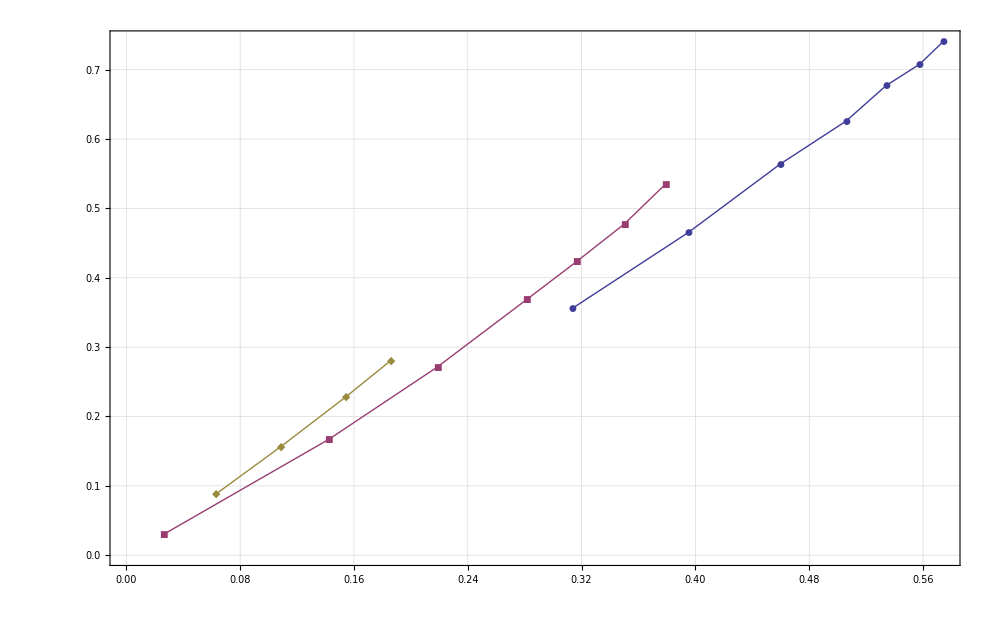

```mathematica
ListPlot[Table[Map[{magicGraham[#[[1]]],#[[2]]}&, Select[vals,Length[#[[1]]]== l &]], {l,2,5}],  PlotMarkers->Automatic, Joined->True, ImageSize->1000, Frame->True, GridLines->Automatic]
```